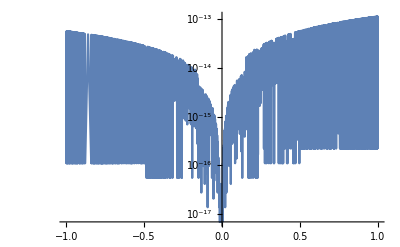

```mathematica
f[x_,ϵ_]=DSolveValue[{ϵ y''[x]+x y'[x]-y[x]==0,y[-1]==1,y[1]==2},y[x],x];
fi[x_,ϵ_]=ϵ^(1/2)(-x/ϵ^(1/2)+3/(√(2π))(ⅇ^((-(x/ϵ^(1/2))^2)/2)+x/ϵ^(1/2)∫_(-∞)^(x/ϵ^(1/2)) ⅇ^(-t^2/2)ⅆt));
LogPlot[{Abs[f[x,0.001]-fi[x,0.001]]},{x,-1,1}]
```

```mathematica
fi[1,.01]//FullSimplify
```

2.

```mathematica
RealAbs[f[x,ϵ]]//FullSimplify
```

$Aborted

```mathematica
DSolveValue[{y''[ξ]+ξ y'[ξ]==0},y[ξ],ξ]
```

C[2]+√(π/2) C[1] Erf[ξ/(√2)]

```mathematica
DSolveValue[
{s'[t]==0,
c'[t]==s[t]-(κ+s[t])c[t],
s[0]==1,
c[0]==0},{s[t],c[t]},t]//FullSimplify
```

{1,(1-ⅇ^(-t (1+κ)))/(1+κ)}

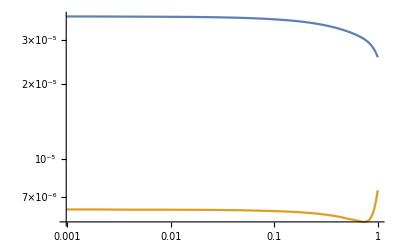

```mathematica
Module[{μ,κ,ϵ,sc,cc,st,ct},
μ=1/2;
κ=1;
ϵ=0.0001;
sc[t_]=κ ProductLog[1/κ ⅇ^(-t+μ/κ t+1/κ)];
cc[t_]=-1/(κ+1)ⅇ^(-(κ+1)t/ϵ)+(κ ProductLog[1/κ ⅇ^(-t+μ/κ t+1/κ)])/(κ+κ ProductLog[1/κ ⅇ^(-t+μ/κ t+1/κ)]);
{st[t_],ct[t_]}=NDSolveValue[
{s'[t]==-s[t]+(μ+s[t])c[t],
ϵ c'[t]==s[t]-(κ+s[t])c[t],
s[0]==1,
c[0]==0},{s[t],c[t]},{t,0,0.5}];
LogLogPlot[{Abs[sc[t]-st[t]],Abs[cc[t]-ct[t]]},{t,0,1}]]
```

```mathematica
∫_(-∞)^x ⅇ^(-t^2/2)ⅆt
```

√(π/2) (1+Erf[x/(√2)])

```mathematica
DSolveValue[
{y0''[ζ]+ζ y0'[ζ]-y0[ζ]==0},
y0[ζ],ζ]//FullSimplify
Asymptotic[DSolveValue[
{y0''[ζ]+ζ y0'[ζ]-y0[ζ]==0},
y0[ζ],ζ]/.{C[1]->1/2,C[2]->-3/(√(2π))}//FullSimplify,{ζ,-∞,1}]
```

ζ C[1]-ⅇ^(-ζ^2/2) C[2]-√(π/2) ζ C[2] Erf[ζ/(√2)]

-ζ

```mathematica
Solve[
{ζ C[1]-√(π/2) ζ C[2]==2ζ,ζ C[1]+√(π/2) ζ C[2]==-ζ},
{C[1],C[2]}]
```

{{C[1]→1/2,C[2]→-3/(√(2 π))}}

```mathematica
lim_(x->-∞) Erf[x]
```

-1

```mathematica
Asymptotic[1/2 x+3/(√(2π))(ⅇ^(-x^2/2)+x √(π/2) (1+Erf[x/(√2)])),x->∞]
```

(7 x)/2

```mathematica
C[1]x-C[2](ⅇ^(-x^2/2)+x∫_(-∞)^x ⅇ^(-t^2/2)ⅆt)
```

x C[1]-C[2] (ⅇ^(-x^2/2)+√(π/2) x (1+Erf[x/(√2)]))

```mathematica
Assuming[t>0,1/(√(4π t))∫_(-∞)^∞ ⅇ^((-(η-y)^2)/(4t))Piecewise[{{uL, y<0}, {uR, y>0}}]ⅆy//FullSimplify]
```

1/2 (uR+uR Erf[η/(2 √t)]+uL Erfc[η/(2 √t)])

```mathematica
u0[η_]=Piecewise[{{uL, η<0}, {uR, η>0}}];
ϕ[x_]=1/(√(4π t))ⅇ^(-x^2/(4t));
Assuming[t>0,Convolve[u0[y],ϕ[y],y,η]]
```

1/2 (uR+uR Erf[η/(2 √t)]+uL Erfc[η/(2 √t)])

```mathematica
DSolveValue[{η^3 y0'[η]==η y0[η]^2},y0[η],η]
```

-η/(-1+η C[1])

```mathematica
DSolveValue[{η^3 y1'[η]==(η+2)η^2/(1-C[1]η)^2+2 η^2/(1-C[1]η)y1[η]},y1[η],η]/.{C[1]->-1,C[2]->0}//FullSimplify
```

-1/(1+η)

```mathematica
Asymptotic[AsymptoticDSolveValue[{x^3 y'[x]==ϵ((1+ϵ)x+2 ϵ^2)y[x]^2,y[1]==1-ϵ},y[x],x,{ϵ,0,1}],x->-∞]
AsymptoticDSolveValue[{η^3 y'[η]==((1+ϵ)η+2ϵ)y[η]^2},y[η],η,ϵ->0]
```

1

(ϵ (-1-η))/(-1+η C[1])^2-η/(-1+η C[1])

```mathematica
Series[(1-ϵ/x)/.x->ϵ η,{ϵ,0,1}]
Series[(η/(1-C[1]η)+ϵ (C[2] η^2-η-1)/(1-C[1] η^2))/.η->x/ϵ,{ϵ,0,1}]
```

1-1/η

-1/C[1]+((-1-x C[1] C[2]) ϵ)/(x C[1]^2)+O[ϵ]^2

```mathematica
Series[(η/(1+η)-ϵ 1/(1+η))/.η->x/ϵ,{ϵ,0,2}]
```

1-ϵ/x+(1/x^2-1/x) ϵ^2+O[ϵ]^3

```mathematica
Series[1/(1+η),{η,∞,3}]
```

1/η-(1/η)^2+(1/η)^3+O[1/η]^4

```mathematica
AsymptoticDSolveValue[ϵ ζ^3 y'[ζ]==((1+ϵ)ζ+2)y[ζ]^2,y[ζ],ζ,{ϵ,0,2}]
```

(ϵ ζ^2)/(1+ζ)+(ϵ^2 ζ^3 (-1+ζ C[1]))/(1+ζ)^2

```mathematica
DSolveValue[ζ^3 y0'[ζ]==(ζ+2)y0[ζ]^2,y0[ζ],ζ]//FullSimplify
```

ζ^2/(1+ζ-ζ^2 C[1])

```mathematica
Series[(η/(1+η)-ϵ 1/(1+η))/.η->ϵ ζ,{ϵ,0,2}]
```

(-1+ζ) ϵ+(ζ-ζ^2) ϵ^2+O[ϵ]^3

```mathematica
Series[(ϵ ζ^2/(1+ζ-ζ^2 C[1]))/.ζ->η/ϵ,{ϵ,0,1}]
```

-ϵ/C[1]+O[ϵ]^2